```mathematica
f[a_,b_,k1_,k2_,k3_]:= k1*a*a*b+k2-k3*a
```

```mathematica
g[a_,b_,k1_,k2_,k4_]:= -k1*a*a*b+k4
```

```mathematica
{k1=0.0004, k2=50, k3=10, k4=25}
```

{0.0004,50,10,25}

```mathematica
{aBar = (k2+k4)/k3,bBar = k4/(k1*aBar^2)}
```

{15/2,1111.11}

```mathematica
J={{2*k1*aBar*bBar-k3,k1*aBar^2},{-2*k1*aBar*bBar,-k1*aBar}}
```

{{-3.33333,0.0225},{-6.66667,-0.003}}

```mathematica
Eigenvalues[J]
```

{-3.28767,-0.0486667}

```mathematica
k4=100
```

100

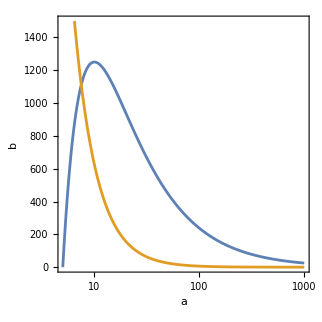

```mathematica
p1 = ContourPlot[{f[a,b,k1,k2,k3]==0,g[a,b,k1,k2,k4]==0},{a,5,1000},{b,0,1500},ScalingFunctions->{"Log",None},PlotPoints->200,FrameLabel->{a,b}]
```

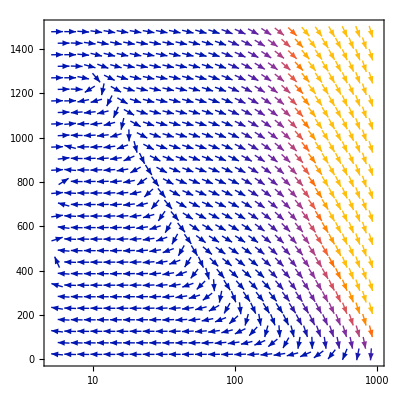

```mathematica
p2 = VectorPlot[{f[a,b,k1,k2,k3],g[a,b,k1,k2,k4]},{a,5,1000},{b,0,1500},ScalingFunctions->{"Log",None},VectorPoints->Fine]
```

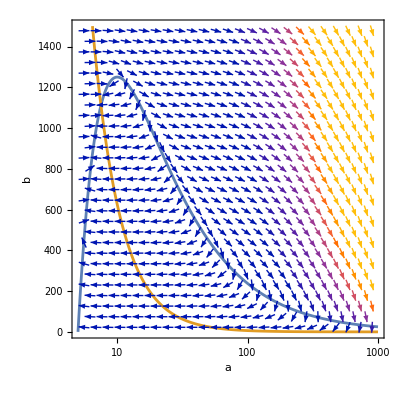

```mathematica
Show[p1,p2]
```